```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/

```mathematica
(* Thickness *)
th=0.003;
```

## Hamiltonians

### Definitions

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
hp[3,tw,ts]//MatrixForm
```

(0 | 0 | tw | ts | 0
0 | 0 | 0 | tw | ts
tw | 0 | 0 | 0 | tw
ts | tw | 0 | 0 | 0
0 | ts | tw | 0 | 0)

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with antiperiodic bc *)
ha[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->-tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with e^ik bc *)
hk[k_,n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->Exp[I k]tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with free bc *)
ω=N [(Sqrt[5]-1)/2];
rot=28; (* rotate the sequence of couplings *)
fib[n_]:=IntegerPart[ω( n+1+rot)]-IntegerPart[ω (n+rot)];
jump[n_,tw_,ts_]:=If[fib[n-1]<1,ts,tw];

hf[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with periodic bc *)
hpn[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
AppendTo[tbl,{1,F2}->tw];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

### Tests

```mathematica
(* wavefunctions in the co-basis, ordered by IDoS label *)
wf=Block[{val,vec,i=9,ts=10.,tw=1.},
{val,vec}=Eigensystem[hp[i,tw,ts]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

```mathematica
MatrixPlot [Abs[wf]^2,FrameLabel->{"energy label","co-number label"},PlotLabel->"Amplitude labelled by co-number and energy",PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

-Graphics-

According to the perturbative theory, the highest eigenvalue is E_max = 1/(1-ρ/2).
The agreement with numerics is quite poor.

```mathematica
Block[{ρ=0.1,n=16},
{Sort[Eigenvalues[hp[n,ρ,1.]]][[-1]],1/(1-ρ/2)}]
```

{1.0584,1.05263}

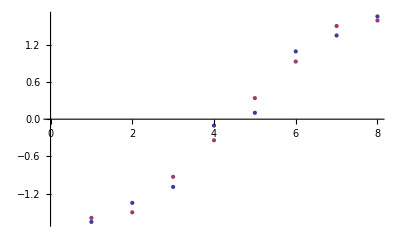

```mathematica
Block[{ts=.5,tw=1.,vpp,vpa,i=4},
vpp=Sort@Eigenvalues[hp[i,tw,ts]];
vpa=Sort@Eigenvalues[ha[i,tw,ts]];
ListPlot[{vpp,vpa},Joined->False,PlotStyle->Thickness[0.005]]
]
```

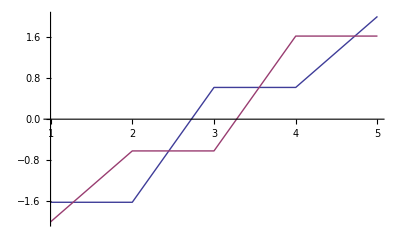

```mathematica
Block[{mp,ma,vpp,vpa,i=3},
mp=Table[DiscreteDelta[j-k+1]+DiscreteDelta[j-k+Fibonacci[i+2]-1],{j,Fibonacci[i+2]},{k,Fibonacci[i+2]}];
mp=mp+Transpose@mp;
ma=Table[DiscreteDelta[j-k+1]-DiscreteDelta[j-k+Fibonacci[i+2]-1],{j,Fibonacci[i+2]},{k,Fibonacci[i+2]}];
ma=ma+Transpose@ma;
vpp=Sort[Eigenvalues[mp]//N];
vpa=Sort[Eigenvalues[ma]//N];
ListPlot[{vpp,vpa},Joined->True]
]
```

## Partition function

### Spectrum: definitions.

Note that the effective bands are the largest when tw = ts. In that case and for q ≤ 1 all fractal dimensions should be equal to 1 (and therefore τ(q ≤ 1) = q-1), whereas for we should have τ(q ⟩ 1) = q/2. Numerically, the convergence using our effective bandwidths is very slow, and the larger q gets, the slower the convergence is. This is probably because the bands are so large in that case. 
I do hope that the smaller tw/ts is, the faster the convergence will be!

```mathematica
(* Compute the fractal dimension Subscript[D, q0] for a system of size fib(i+2) *)
Clear[FractalD];
FractalD[i_,tw_,ts_,q0_]:=Block[{vpp,vpa,vppN,vpaN,bandlist,bandlistN,gam,gamN,τ0,τ,q},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i,tw,ts]]];
vpa=Sort[Eigenvalues[ha[i,tw,ts]]];
(* spectres des systèmes de taille i+1 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+1,tw,ts]]];
vpaN=Sort[Eigenvalues[ha[i+1,tw,ts]]];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
(* calcul des fonctions de partition Subscript[Γ, i] et Subscript[Γ, i+1] *)
gam=Fibonacci[i+2]^-q Plus@@((bandlist)^-τ);
gamN=Fibonacci[i+3]^-q Plus@@((bandlistN)^-τ);
(* Subscript[D, q0] *)
τ0=τ/.FindRoot[(gamN/gam/.q->q0)-1,{τ,1.}];
τ0
]
```

On a τ(q > 2) =q/2 et τ(q ≤ 2) = q-1 quand t_w=t_s. → singularités de van Hove !

```mathematica
FractalD[13,1.,1.,4]
```

2.

```mathematica
FractalD[13,.1,1.,20]
```

6.00068

Because Γ^(n+1)/Γ^n=ω^q((Σ(Δ^(n+1)))^(-τ(q)))/((Σ(Δ^n))^(-τ(q)))=1 it is hard to compute τ(q) but easy to get q(τ).
We have
q(τ) = (B^n(τ)-B^(n+1)(τ))/(Log(q))
where
B^n(τ)=Log[(Σ(Δ^n))^-τ]

Next, we want to compute f-α. Easy!
α(τ)=(q'(τ))^-1
and
f(α(τ)) = q(τ)α(τ) - τ

For q<0, it seems to converge way better if we compute Γ^(n+2)/Γ^n rather than Γ^(n+1)/Γ^n. Why?

```mathematica
(* Return banlists *)
BandLists[i_,tw_,ts_]:=Block[{vpp,vpa,vppN,vpaN,bandlist,bandlistN},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i,tw,ts]]];
vpa=Sort[Eigenvalues[ha[i,tw,ts]]];
(* spectres des systèmes de taille i+1 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+1,tw,ts]]];
vpaN=Sort[Eigenvalues[ha[i+1,tw,ts]]];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
{bandlist,bandlistN}
]
```

```mathematica
(* Plot τ -> {α(τ),f(α(τ))} *)
Clear[FractalFa];
FractalFa[τmin_,τmax_,bandlist_,bandlistN_]:=Block[{q,alpha,f,om=N[2/(1+√5)]},
(* q(τ) *)
q=Log[Plus@@((bandlist)^-τ)/Plus@@((bandlistN)^-τ)]/Log[om];
(*Print[ParametricPlot[{q,τ},{τ,-10,10},AxesLabel->{"q","τ(q)"}]];*)
alpha=1./D[q,τ];
ParametricPlot[{alpha,alpha q-τ},{τ,τmin,τmax},AspectRatio->1,PlotRange->All,AxesLabel->{"α","f(α)"}]
]
```

In the ρ = 1 case, we find two possible values for α:
α(q > 2) = 1/2
α(q ≤ 2) = 1
and for f:
f(1/2) = 0
f(1) = 1

Interpretation:
If we call Δ_a^n the a^th bandwidth of the n^th approximant, we have
1/F_n∼ (Δ_a^n)^(α(a)) as n→∞.
Thus, in the ρ=1 case, there is only 2 types of bandwidths, the ones that behave as (1/F_n)^2, giving α=1/2, and the ones that behave as 1/F_n, giving α=1. f(1/2)=0 implies that the bands of width (1/F_n)^2 form a set of 0 Hausdorff dimension (a countable set!).

In the ρ=1 case, we can compute explicitely the bandwidths. We find
Δ_a^n∼ (π/F_n) sin[2 a π/F_n + π/(2 F_n)], a ∈ [0,F_n] 
And indeed, at the edges of the spectrum, Δ_a^n∼π^2/(2 F_n^2). This quadratic behavior is found only at the edges of the spectrum. It is thus the 2 edges that give rise to the α=1/2 exponent. The aformentioned countable set of 0 Hausdorff dimension is thus made of just 2 points. These 2 points are accumulation points for the energy levels!

If we compute numerically the Legendre transform of τ for a finite size system, we find a continuum of values of α ranging from 1/2 to 1.
We check that indeed f(1/2) = 0, f(1) = 1.

```mathematica
{b,bnew}=BandLists[10,1.,1.];
```

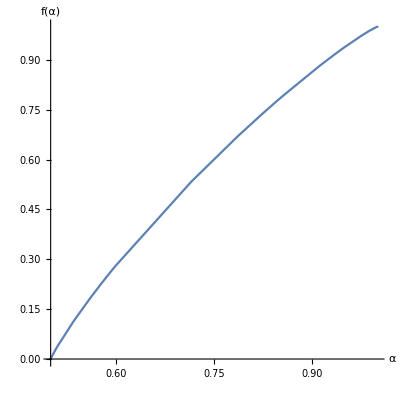

```mathematica
p=FractalFa[-2,50,b,bnew]
```

```mathematica
{b,bnew}=BandLists[14,.1,1.];
```

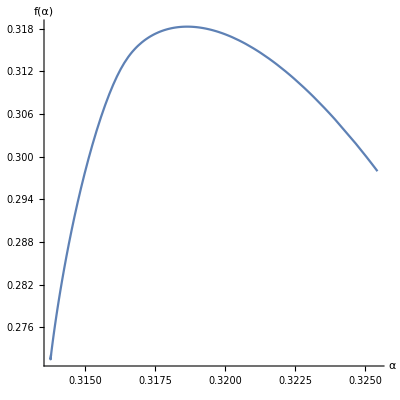

```mathematica
p=FractalFa[-2,12,b,bnew]
```

In the framework of the asymptotic formulas, if ρ < 1/8, α is an increasing function of the parameter x, while it is decreasing in the other case. 
So it seems that the validity of the asymptotic formulas is ρ < 1/8.

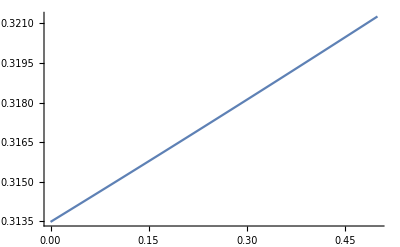

```mathematica
ρ=1/10;
om=N[2/(1+√5)];
z=ρ/2;barz=ρ^2;
α[x_]:=Log[om]/(x Log[z]+(1-2x)/3Log[barz]);
Plot[α[x],{x,0,1/2}]
```

### Spectrum: tests

```mathematica
(* asymptotically exact solution in the ρ->0 limit *)
exactFD[ρ_,q_]:=Block[{ω=1/GoldenRatio,z,barz},
z=ρ/2;
barz=ρ^2;
τ/.FindRoot[2 ω^(2q)z^-τ+ω^(3q)barz^-τ-1,{τ,10}]
]
```

```mathematica
start=2;
stop=16;
d0=ParallelTable[FractalD[i,1/10.,1.,0],{i,start,stop}]
```

Système de taille fib(n), n = 4

Système de taille fib(n), n = 6

Système de taille fib(n), n = 8

Système de taille fib(n), n = 10

Système de taille fib(n), n = 5

Système de taille fib(n), n = 7

Système de taille fib(n), n = 9

Système de taille fib(n), n = 11

Système de taille fib(n), n = 12

Système de taille fib(n), n = 13

Système de taille fib(n), n = 14

Système de taille fib(n), n = 15

Système de taille fib(n), n = 16

Système de taille fib(n), n = 17

Système de taille fib(n), n = 18

{-0.468077,-0.26209,-0.367179,-0.292778,-0.336534,-0.306884,-0.325309,-0.313124,-0.320869,-0.315809,-0.319057,-0.316947,-0.318307,-0.317426,-0.317995}

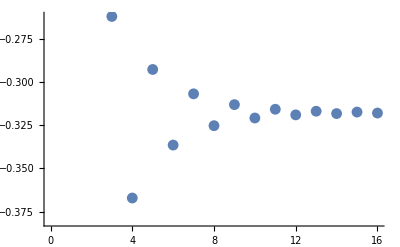

-0.314387

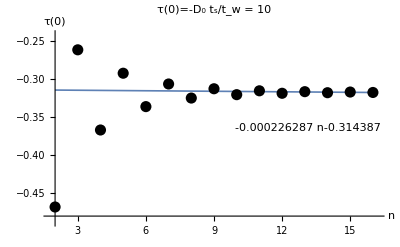

```mathematica
Block[{fit,data,plot},
data=MapThread[{#1,#2}&,{Range[start,stop],d0}];
Print[ListPlot[data]];
fit=LinearModelFit[data[[start+10;;]],n,n];
Print[Normal[fit]/.n->0];
plot=Plot[Normal@fit,{n,start,stop},PlotRange->{{start-0.2,stop+0.2},{Min[d0]-0.02,Max[d0]+0.02}},Epilog->{PointSize@.02,Point@data},AxesLabel->{"n","τ(0)"},PlotLabel->"τ(0)=-D_0 \n t_s/t_w = 10",PlotStyle->Thickness[th],PlotLegends->Placed[Normal@fit,{Right,Center}]];
Print[plot];
(*Export[dir<>"/data/hausdorff.pdf",plot];*)
]
```

```mathematica
start=2;
stop=16;
d2=ParallelTable[FractalD[i,1/2.,1.,2],{i,start,stop}]
```

Système de taille fib(n), n = 4

Système de taille fib(n), n = 6

Système de taille fib(n), n = 8

Système de taille fib(n), n = 10

Système de taille fib(n), n = 5

Système de taille fib(n), n = 7

Système de taille fib(n), n = 9

Système de taille fib(n), n = 11

Système de taille fib(n), n = 12

Système de taille fib(n), n = 13

Système de taille fib(n), n = 14

Système de taille fib(n), n = 15

Système de taille fib(n), n = 16

Système de taille fib(n), n = 17

Système de taille fib(n), n = 18

{0.72461,0.605398,0.679505,0.631598,0.664941,0.640894,0.658364,0.645304,0.654958,0.647685,0.653101,0.649019,0.652069,0.649773,0.651492}

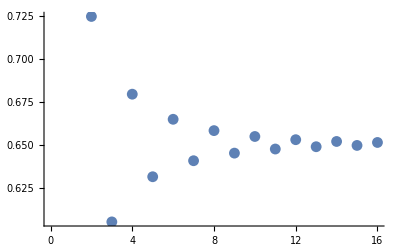

0.655441

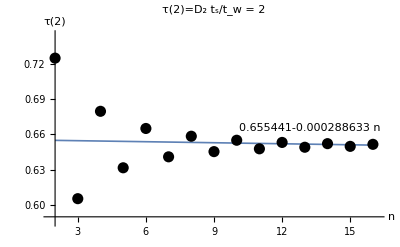

```mathematica
Block[{fit,data,plot},
data=MapThread[{#1,#2}&,{Range[start,stop],d2}];
Print[ListPlot[data]];
fit=LinearModelFit[data[[start+11;;]],n,n];
Print[Normal[fit]/.n->0];
plot=Plot[Normal@fit,{n,start,stop},PlotRange->{{start-0.2,stop+0.2},{Min[d2]-0.02,Max[d2]+0.02}},Epilog->{PointSize@.02,Point@data},AxesLabel->{"n","τ(2)"},PlotLabel->"τ(2)=D_2 \n t_s/t_w = 2",PlotStyle->Thickness[th],PlotLegends->Placed[Normal@fit,{Right,Center}]];
Print[plot];
(*Export[dir<>"/data/renyi_entropy_2.pdf",plot];*)
]
```

```mathematica
start=2;
stop=16;
d20=ParallelTable[FractalD[i,1/2.,1.,20],{i,start,stop}]
```

Système de taille fib(n), n = 4

Système de taille fib(n), n = 6

Système de taille fib(n), n = 8

Système de taille fib(n), n = 10

Système de taille fib(n), n = 5

Système de taille fib(n), n = 7

Système de taille fib(n), n = 9

Système de taille fib(n), n = 11

Système de taille fib(n), n = 12

Système de taille fib(n), n = 13

Système de taille fib(n), n = 14

Système de taille fib(n), n = 15

Système de taille fib(n), n = 16

Système de taille fib(n), n = 17

Système de taille fib(n), n = 18

{11.208,8.64141,10.3762,8.72053,10.2621,8.7331,10.2458,8.73509,10.2434,8.7354,10.2431,8.73545,10.243,8.73546,10.243}

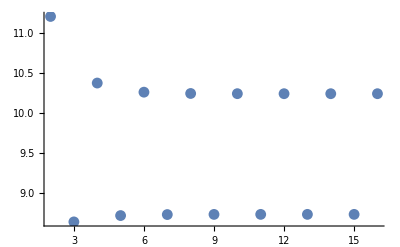

10.24728.73466

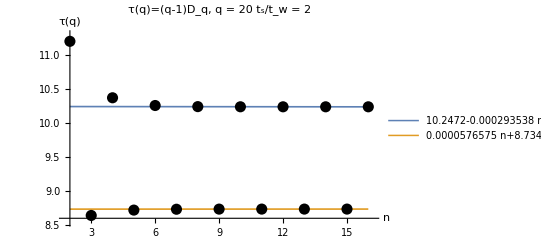

```mathematica
Block[{fit,data,plot},
data=MapThread[{#1,#2}&,{Range[start,stop],d20}];
Print[ListPlot[data,PlotRange->All]];
fitSup=LinearModelFit[data[[start+5;;;;2]],n,n];
fitInf=LinearModelFit[data[[start+6;;;;2]],n,n];
Print[Normal[fitSup]/.n->0,Normal[fitInf]/.n->0];
plot=Plot[{Normal@fitSup,Normal@fitInf},{n,start,stop},PlotRange->{{start-0.2,stop+0.2},{Min[d20]-0.1,Max[d20]+0.1}},Epilog->{PointSize@.02,Point@data},AxesLabel->{"n","τ(q)"},PlotLabel->"τ(q)=(q-1)D_q, q = 20 \n t_s/t_w = 2",PlotStyle->Thickness[th],PlotLegends->Placed[{Normal@fitSup,Normal@fitInf},{Right,Center}]];
Print[plot];
Export[dir<>"/data/renyi_q20_2.pdf",plot];
]
```

### Wavefunctions: definitions.

We define general functions computing fractal dimensions from lists, rather than functions adapted to our specific case.

We compute χ_q^n(i)=Σ_a|ψ^n(i,a)|^(2q).
We define the local dimension of the wavefunctions:
D_q(i)=lim_(n→∞) 1/(q-1)(log(χ_q^n(i)))/(log(1/F_n))

```mathematica
(* wf is a list of numbers that are a priori the coefficients of a wavefunction. They can be coefficients in the position basis, for a given energy, or coefficients in the energy basis for a particular position. *)
WfD[wf_,q_]:=-(q-1)^-1 Log[Plus@@(Abs[wf]^(2q))]/Log[Length@wf]
```

We compute the partition function (Γ_(τ,q))^n(i)=Σ_a(|ψ^n(i,a)|^(2q))/((Δ_a^n)^τ).
We define the local dimension of the wavefunctions:
τ_i(q) such that lim_(n→∞) ((Γ_(τ_i(q),q))^(n+1)(i))/((Γ_(τ_i(q),q))^n(i))=1

```mathematica
(* compute fractal dimension Subscript[D, q] from 2 lists of weights and box lengths, using the thermodynamic formalism *)
PartD[weights_,weightsN_,lengths_,lengthsN_,q_]:=Block[{gam,gamN,τ,τ0,q0},
gam=Plus@@((weights)^q0(lengths)^-τ);
gamN=Plus@@((weightsN)^q0(lengthsN)^-τ);
(* Subscript[D, q] *)
τ0=τ/.FindRoot[(gamN/gam/.q0->q)-1,{τ,0}];
τ0/(q-1)
]
```

### Wavefunctions: tests.

#### Tree structure

After a renormalization step, a given site i of the n^th approximant becomes either molecular (in which case n becomes n-2) or atomic (n becomes n-3). 
We can thus associate to each site a unique “renormalization path”: the sequence of molecular/atomic sites that has led to it, starting from the trivial (F_n=1) chain and inflating it.

More details in the “renormalization_path.nb” file.

```mathematica
(* take a renormalization path (seq), a site label (i) and an approximant size (n) and return the new renormalization path, the new site label and the new size after one renormalization group operation *)
ClearAll[i,n];
iterSeq[{seq_,i_,n_}]:=Block[{inew=i,seqn=seq,nnew=n},
If[i>Fibonacci[n-1],seqn="m"<>seq;inew=i-Fibonacci[n-1];nnew=n-2;,
If[i>Fibonacci[n-2],seqn="a"<>seq;inew=i-Fibonacci[n-2];nnew=n-3,
seqn="m"<>seq;nnew=n-2;]];
{seqn,inew,nnew}
]

(* false when n<3 *)
test=#[[3]]≥3&;
(* take a site (i), a size (n) and return the renormalization path for this site *)
path[i_,n_]:=NestWhile[iterSeq,{"",i,n},test][[1]]->i
(* compute the relative time spent on molecular sites (x) *)
xPath[i_,n_]:={i,StringCount[NestWhile[iterSeq,{"",i,n},test][[1]],"m"]/n}
(* generate the whole (x) tree! *)
tree[n_]:=xPath[#,n]&/@ Range[Fibonacci[n]]
```

```mathematica
paths[n_]:=path[#,n]&/@Range[Fibonacci[n]]
```

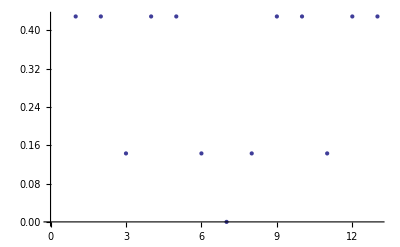

```mathematica
ListPlot[tree[7],Joined->False]
```

#### D^μ(i) and D^μ(a)

```mathematica
(* D^μ coincidence check: we should find the dimensions of the spectrum if we give 1/Subscript[F, n] as a weight *)
n=13;
q=0;
{l,lN}=BandLists[n,.1,1.];
{w,wN}={Table[1/Fibonacci[n+2],{Fibonacci[n+2]}],Table[1/Fibonacci[n+3],{Fibonacci[n+3]}]};
(q-1)PartD[w,wN,l,lN,q]
FractalD[n,.1,1.,q]
```

-0.316947

-0.316947

```mathematica
(* D^μ ρ ≃ 1 check *)

ρ=1.;
n=10;
(* the Fibonacci chain has "period" 3 *)
nN=n+3;
q=20;

(* eigenvalues for periodic bc, and associated wavefunctions *)
{valp,vec}=Eigensystem[hp[n,ρ,1.]];
(*order wavefunctions by increasing energy*)
wlist=Abs[vec[[Ordering[valp]]]]^2;
(* eigenvalues for antiperiodic bc *)
vala=Sort[Eigenvalues[ha[n,ρ,1.]]];
(* bands *)
l=MapThread[Abs[#1-#2]&,{vala,valp}];

(* eigenvalues for periodic bc, and associated wavefunctions *)
{valp,vec}=Eigensystem[hp[nN,ρ,1.]];
(*order wavefunctions by increasing energy*)
wlistN=Abs[vec[[Ordering[valp]]]]^2;
(* eigenvalues for antiperiodic bc *)
vala=Sort[Eigenvalues[ha[nN,ρ,1.]]];
(* bands *)
lN=MapThread[Abs[#1-#2]&,{vala,valp}];

a=IntegerPart[Fibonacci[n+2]/2];
aN=IntegerPart[Fibonacci[nN+2]/2];
a=-1;
aN=-1;
(* summing over SITES at fixed energy *)
(q-1)PartD[wlist[[a]],wlistN[[aN]],l,lN,q]
```

10.0001

#### D(i) and D(a)

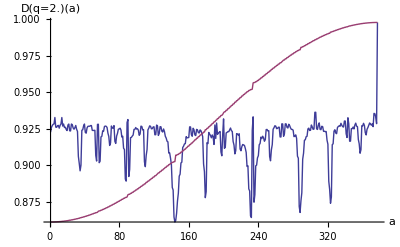

```mathematica
(* ρ ≃ 1 check *)
(* increasing precisions does not provoke noticable changes, howevever increasing the number of sites does. *)
ρ=.9;
n=12;
q=2.;
tol=10^-14;
{val,vec}=Eigensystem[hp[n,ρ,1.]];
(*order wavefunctions by increasing energy*)
vec=vec[[Ordering[val]]];
(* drop small components *)
vecn=Chop[vec,tol];
(* here we compute the USUAL fratal dimensions of the wf *)
l=WfD[#,q]&/@vecn;

(* Plot the wf dimensions as a function of the energy label, with the spectrum superimposed; we see that the most localized states are close to the largest gaps, while the most extended ones are close the the edges *)
val=Sort[val];
val=(Max[l]-Min[l])/(Max[val]-Min[val])(val-val[[1]])+Min[l];
ListPlot[{l,val},PlotRange->All,PlotStyle->PointSize[.01],Joined->True,AxesLabel->{"a","D(q="<>ToString[q]<>")(a)"}]
(*Export[dir<>"data/local_dim_wf_rho_20.png",%,ImageResolution->200]*)
```

```mathematica
(* rescale the spectrum between 0 and 1 *)
val=(val-Min[val])/(Max[val]-Min[val]);
L=Length[val];
idos=Table[{val[[i]],i/L},{i,L}];
```

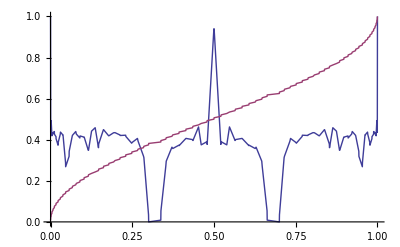

```mathematica
(* rescale the fractal dimensions between 0 and 1 *)
l=(l-Min[l])/(Max[l]-Min[l]);
(* dimensions as a function of the energy *)
l=MapThread[{#1,#2}&,{val,l}];
ListPlot[{l,idos},Joined->True]
```

```mathematica
(* ρ << 1 check *)
ρ=1./10;
n=13;
i=IntegerPart[Fibonacci[n+2]/2];
q=20;
tol=10^-14;
{val,vec}=Eigensystem[hp[n,ρ,1.]];
(*order wavefunctions by increasing energy*)
vec=vec[[Ordering[val]]];
(* drop small components *)
vecn=Chop[vec,tol];
l=WfD[#,q]&/@Transpose[vecn];
```

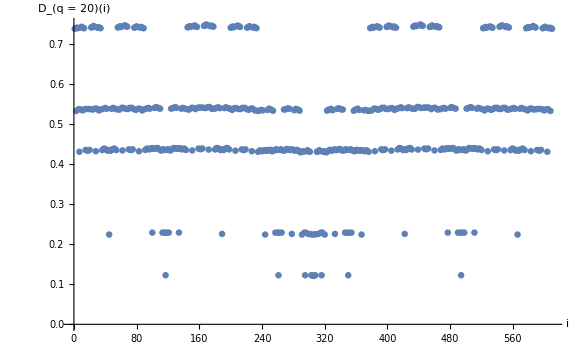

```mathematica
m=Max[l];
ListPlot[l,PlotRange->All,PlotStyle->PointSize[.008],Joined->True,ColorFunction->Function[{x,y},ColorData["ThermometerColors"][y/(1.5m)]],AxesLabel->{"i","D_(q = 20)(i)"}]/.Line->Point
(*Export[dir<>"data/local_dim_wf_rho_20.png",%,ImageResolution->200]*)
```

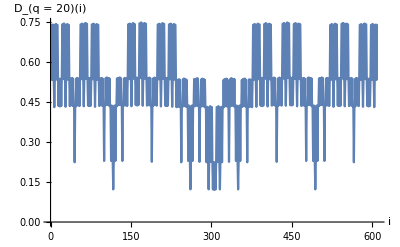

```mathematica
m=Max[l];
ListPlot[l,PlotRange->All,PlotStyle->PointSize[.008],Joined->True,AxesLabel->{"i","D_(q = 20)(i)"}]
(*Export[dir<>"data/local_dim_wf_rho_20_joined.png",%,ImageResolution->200]*)
```

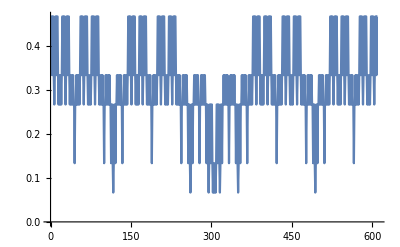

```mathematica
ListPlot[tree[n+2],Joined->True]
```

```mathematica
(* symptotic analytical expression for tilde D *)
ω=N[(√5-1)/2];
WfDTh[x_,y_,q_,ρ_]:=(x Log[0.5]-q/(q-1)(4-5x)/6 ρ^2-1/(q-1)(-x+2y)ρ^(2q))/Log[ω]
```

```mathematica
(* symptotic analytical expression for tilde D *)
WfDTh3[x_,q_,ρ_]:=(x Log[0.5]-q/(q-1)(4-5x)/6 ρ^2)/Log[ω]
```

```mathematica
WfDTh4[x_,ρ_]:=x Log[0.5]/Log[ω]
```

Slight modification of the theoretical expression, attempting to take into account the finite - size effect.

```mathematica
(* asymptotic expression in the limit ρ = 0, for a size Subscript[F, n+2] system *)
asymD[x_,n_]:=x ((n+2)Log[2.])/Log[Fibonacci[n+2]]
WfDTh3[n_,x_,q_,ρ_]:=(n+2)(x Log[0.5]-q/(q-1)(4-5x)/6 ρ^2)/(-Log[Fibonacci[n+2]])
```

```mathematica
λ[ρ_]:=1/(2+ρ^2);
λb[ρ_]:=1/(1+2 ρ^2);
cq[ρ_,q_]:=1+ρ^(2q);
sq[ρ_,q_]:=1+ρ^(2q);
WfDTh2[x_,y_,q_,ρ_]:=1/Log[ω](q/(q-1)x Log[λ[ρ]]+(1-2x)/3 Log[λb[ρ]]-1/(q-1)((x-y)Log[1/(2cq[ρ,q])]+y Log[1/(2sq[ρ,q])]))
```

Suppose the renormalization factor of the molecular states λ writes
λ = 1/2 1/(1+a ρ^2)
Normally, a =1/2.

```mathematica
Dthtest[n_,x_,q_,ρ_,a_]:=(n+2)(x Log[0.5]-q/(q-1)(2/3-(4/3-a)x)ρ^2)/(-Log[Fibonacci[n+2]])
```

```mathematica
(* ρ << 1 check *)
ρ=1/10.;
n=12;
i=IntegerPart[Fibonacci[n+2]/2];
q=20;
tol=10^-14;
{val,vec}=Eigensystem[hp[n,ρ,1.]];
(*order wavefunctions by increasing energy*)
vec=vec[[Ordering[val]]];
(* drop small components *)
vecn=Chop[vec,tol];
DxList=WfD[#,q]&/@vecn;
```

For a given ρ, q>0 and system size n, compute the D^x(x) dimensions, ie the D^x(i) dimensions averaged on all sites having the same x.

```mathematica
ClearAll[n,ρ,q,val,vec,DxList,xlist,xvalues,listPos,avDx,tol];
avDx[ρ_,q_,n_]:=Block[{val,vec,DxList,xlist,xvalues,listPos,avDx,tol=10^-14,avDxNorm},
(* compute wavefunctions and energies *)
{val,vec}=Eigensystem[hp[n,ρ,1.]];
(*order wavefunctions by increasing energy*)
vec=vec[[Ordering[val]]];
(* drop small components *)
vec=Chop[vec,tol];
(* list fractal dimensions, indexed by site *)
DxList=WfD[#,q]&/@Transpose[vec];

(* compute x for each site *)
xlist=tree[n+2];
(* drop the site labels, they are unecessary as x is indexed by increasing x label *)
xlist=Last@(Transpose[xlist]);

(* list all possible values of x *)
xvalues=Sort@DeleteDuplicates[xlist];
(* list all positions by increasing value of x *)
listPos=Flatten[Position[xlist,#]]&/@xvalues;
(* for each value of x compute the average - on positions corresponding to this x - fractal dimension *)
avDx=Mean[DxList[[#]]]&/@listPos;
avDxNorm=avDx-(asymD[#,n]&/@xvalues);
(* return the average fractal dimension as a function of x *)
avDx=MapThread[{#1,#2}&,{xvalues,avDx}];
avDxNorm=MapThread[{#1,#2}&,{xvalues,avDxNorm}];
{avDx,avDxNorm}
]
```

```mathematica
n=14;
q=3.;
ρ=0.1;
lbl={"x","D^x(q="<>ToString[q]<>",ρ="<>ToString[ρ]<>")"};
{avd,avdNorm}=avDx[ρ,q,n];
```

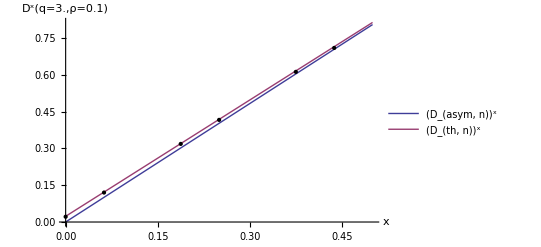

```mathematica
Plot[{asymD[x,n],WfDTh3[n,x,q,ρ]},{x,0,1/2},Epilog->{PointSize[Medium],Point@avd},AxesLabel->lbl,PlotLegends->{"(D_(asym,  n))^x","(D_(th,  n))^x"}]
```

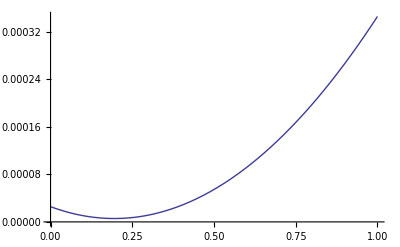

```mathematica
xlist=Sort@DeleteDuplicates[Last@(Transpose[tree[n+2]])];
Plot[Plus@@((Transpose[(Dthtest[n,#,q,ρ,a]&/@xlist-avd)][[2]])^2),{a,0.,1.}]
```

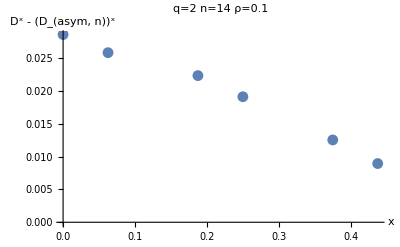

```mathematica
lblNorm={"x","D^x - (D_(asym,  n))^x"};
ListPlot[avdNorm,AxesLabel->lblNorm,PlotLabel->"q="<>ToString[q]<>" n="<>ToString[n]<>" ρ="<>ToString[ρ]]
```

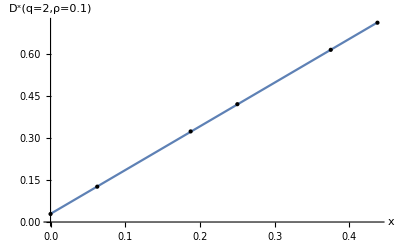

```mathematica
dat=avd;
m=Min[Transpose[avd][[1]]];
mm=Max[Transpose[avd][[1]]];
fit=LinearModelFit[dat,x,x];
Plot[Normal[fit],{x,m,mm},Epilog->{PointSize[Medium],Point@dat},AxesLabel->lbl]
```

```mathematica
(* q dependance *)
ql={2,10,100};
ρ=0.1;
lbl={"x","D^x(q,ρ="<>ToString[ρ]<>")"};
avdl=ParallelMap[avDx[ρ,#,14]&,ql];
```

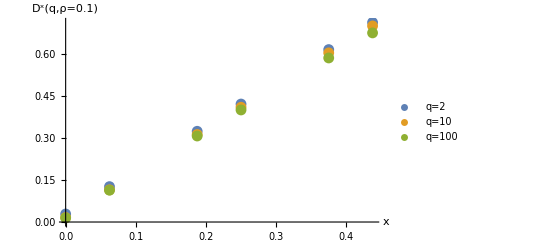

```mathematica
ListPlot[avdl,AxesLabel->lbl,PlotLegends->("q="<>ToString@#&)/@ql]
```

```mathematica
(* a list to contain them all (the fit coefficients as a function of ρ) *)
coefRho={};
```

```mathematica
(* returns the coefficients {b,a} of the affine fit dat(x) = a x + b *)
coeffs[dat_]:=Normal[(LinearModelFit[dat,x,x])["ParameterTable"]][[1,2;;3,2]]
```

```mathematica
δlist=Range[1,5,0.2];
(* make a list of values of ρ, for which we are going to compute the Dx's *)
ρlist=2^-δlist;
q=20;n=14;
(* compute the Dx's for each value of ρ, return the list *)
Dxlist=ParallelMap[avDx[#,q,n]&,ρlist];
(* fit x -> Dx(ρ) linearly, return the list of the coeffs {b,a} such that Dx(ρ) = a(ρ) x + b(ρ) *)
listcoeffs=coeffs/@Dxlist;
```

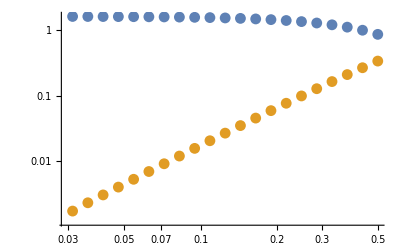

```mathematica
rhoB=MapThread[{#1,#2}&,{ρlist,Transpose[listcoeffs][[1]]}];
rhoA=MapThread[{#1,#2}&,{ρlist,Transpose[listcoeffs][[2]]}];
ListLogLogPlot[{rhoA,rhoB}]
```

```mathematica
0.5Log[2]/Log[GoldenRatio]//N
```

0.72021

```mathematica
coeffs[Log[rhoB]]
coeffs[Log[rhoA]]
```

{0.302953,1.90148}

{-0.0251063,-0.17486}

### LDoS: definitions & tests.

```mathematica
gam[p_,l_,q_,tau_]:=Plus@@((p)^q(l)^-tau);
```

Γ^n(i) = Σ_a(|ψ(i,a)|^(2q))/(Δ_a)^τ
In the ρ->0 limit, the partition function no longer depends on i, but only on x. This is great because numerically we want to compute 
Γ^(n+1)/Γ^n(x), which is well defined.

For a size n<∞ system, x takes its values in a discrete set:
n*x ∈ {1,2,4,5,...} if n = 3p -> in that case x takes p values
n*x ∈ {0,1,3,4,...} if n = 3p+1 -> in that case x takes p+1 values
n*x ∈ {0,2,3,5,...} if n = 3p+2 -> in that case x takes p+1 values 

We want to keep x constant btw n and n+1, ie we want
(n_m+Δn_m)/(n+1)=n_m/n which amounts to
Δn_m=x<1/2, so Δn_m=0 seems the best choice (the error is then at most of order 1/n).

```mathematica
(* take a renormalization path (seq), a site label (i) and an approximant size (n) and return the new renormalization path, the new site label and the new size after one renormalization group operation *)
ClearAll[i,n];
iterSeq[{seq_,i_,n_}]:=Block[{inew=i,seqn=seq,nnew=n},
If[i>Fibonacci[n-1],seqn="m"<>seq;inew=i-Fibonacci[n-1];nnew=n-2;,
If[i>Fibonacci[n-2],seqn="a"<>seq;inew=i-Fibonacci[n-2];nnew=n-3,
seqn="m"<>seq;nnew=n-2;]];
{seqn,inew,nnew}
]
```

```mathematica
(* false when n<3 *)
test=#[[3]]≥3&;
(* take a site (i), a size (n) and return the renormalization path for this site *)
path[i_,n_]:=NestWhile[iterSeq,{"",i,n},test][[1]]
(* compute the Subscript[n, m](i) time spent on molecular sites (x) *)
nm[i_,n_]:=StringCount[NestWhile[iterSeq,{"",i,n},test][[1]],"m"]
```

```mathematica
(* n = 3p +1 *)
p=4;
n=3p+1;
nN=n+1;
(* compute Subscript[n, m] x *)
nml=nm[#,n]&/@Range[Fibonacci[n]];
nmlN=nm[#,nN]&/@Range[Fibonacci[nN]];
(* display values of Subscript[n, m] x shared by both systems *)
DeleteDuplicates[Intersection[nml,nmlN]]//Sort
(* choose among these values *)
nmol=3;
(* positions corresponding to this x value, on both systems *)
posl=Position[nml,nmol]//Flatten;
poslN=Position[nmlN,nmol]//Flatten;
```

{0,3,6}

```mathematica
(* compute bandlists and wavefunctions for both systems *)
ts=1.;
tw=0.1;
(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hp[n-2,tw,ts]];
{vpa,wfa}=Eigensystem[ha[n-2,tw,ts]];
o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
(* spectres des systèmes de taille i+1 p et anti-p *)
{vppN,wfpN}=Eigensystem[hp[nN-2,tw,ts]];
{vpaN,wfaN}=Eigensystem[ha[nN-2,tw,ts]];
o=Ordering[vppN];
vppN=vppN[[o]];
wfpN=wfpN[[o]];
o=Ordering[vpaN];
vpaN=vpaN[[o]];
wfaN=wfaN[[o]];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bl=MapThread[Abs[#1-#2]&,{vpa,vpp}];
blN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
(* take the mean wf *)
meanI=Abs[(wfp+wfa)*0.5]^2;
meanIN=Abs[(wfpN+wfaN)*0.5]^2;
meanI=Abs[wfp]^2;
meanIN=Abs[wfpN]^2;
```

Does the Γ^n(q,τ;i) function only depend on x for arbitrary values of q and τ? Well, apparently, no! (In the following plots, one value of x has been chosen, and the corresponding Γ values are shown in red)

```mathematica
qtest=2.;
tautest=0.00087751;
gaml=gam[#,bl,qtest,tautest]&/@Transpose[meanI];
gamlN=gam[#,blN,qtest,tautest]&/@Transpose[meanIN];
```

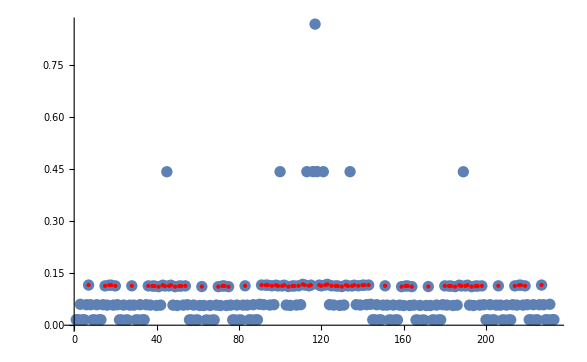

```mathematica
ListPlot[gaml,Epilog->{Red,Point@{#,gaml[[#]]}&/@posl},PlotRange->All]
```

```mathematica
(* evaluate relative error *)
StandardDeviation[gaml[[posl]]]/Mean[gaml[[posl]]]
```

0.0137449

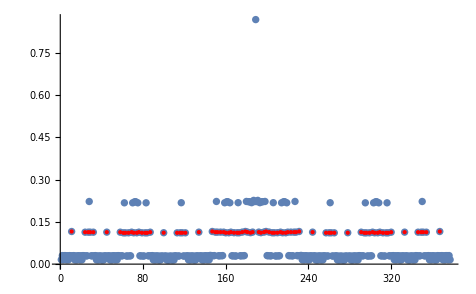

```mathematica
ListPlot[gamlN,Epilog->{Red,Point@{#,gamlN[[#]]}&/@poslN},PlotRange->All]
```

```mathematica
StandardDeviation[gaml[[posl]]/gamlN[[poslN]]]/Mean[gaml[[posl]]/gamlN[[poslN]]]
```

0.00826111

```mathematica
gaml[[posl]]/gamlN[[poslN]]
```

{1.,1.,1.01682,1.01682,1.,1.,1.,1.01682,1.01682,1.,1.0166,1.01742,1.01742,1.0166,1.,1.01682,1.01682,1.,1.,1.,1.01682,1.01682,1.,1.,1.,1.01682,1.01682,1.,1.0166,1.01742,1.01742,1.0166,1.,1.01682,1.01682,1.,1.01661,1.01741,1.01741,1.01677,1.01677,1.01741,1.01741,1.01661,1.,1.01682,1.01682,1.,1.0166,1.01742,1.01742,1.0166,1.,1.01682,1.01682,1.,1.,1.,1.01682,1.01682,1.,1.,1.,1.01682,1.01682,1.,1.0166,1.01742,1.01742,1.0166,1.,1.01682,1.01682,1.,1.,1.,1.01682,1.01682,1.,1.}

Does τ only depends on x? On first approximation, yes!

```mathematica
ClearAll[q,τ];
q=2.;
τxlist=τx/.(FindRoot[gam[Transpose[meanI][[posl[[#]]]],bl,q,τx]/gam[Transpose[meanIN][[poslN[[#]]]],blN,q,τx]-1,{τx,1.}]&/@Range[Length[posl]])
```

{0.00087751,0.00087805,0.00806096,0.00806096,0.000878048,0.00087751,0.000878022,0.0080612,0.00806103,0.000878762,0.00797048,0.00831973,0.00831973,0.00797048,0.000878762,0.00806103,0.0080612,0.00087802,0.00087751,0.000878048,0.00806096,0.00806096,0.00087805,0.00087751,0.00087802,0.00806119,0.00806103,0.000878745,0.00797071,0.00831972,0.00831973,0.00797051,0.000878759,0.00806103,0.00806122,0.000878679,0.00797183,0.00831518,0.00831395,0.00804297,0.00804297,0.00831395,0.00831518,0.00797183,0.000878679,0.00806122,0.00806103,0.000878759,0.00797051,0.00831973,0.00831972,0.00797071,0.000878745,0.00806103,0.00806119,0.00087802,0.00087751,0.00087805,0.00806096,0.00806096,0.000878048,0.00087751,0.00087802,0.0080612,0.00806103,0.000878762,0.00797048,0.00831973,0.00831973,0.00797048,0.000878762,0.00806103,0.0080612,0.000878022,0.00087751,0.000878048,0.00806096,0.00806096,0.00087805,0.00087751}

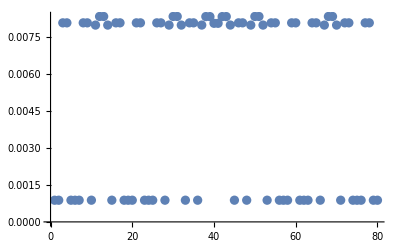

```mathematica
ListPlot[τxlist,PlotRange->All]
```

To a first approximation, Γ^n and one can identify sites having approximately the same x for systems of length n and n+1. Then, τ_num is also approximately only function of x.
Thus, we now average the partition function on sites having the same x, before finding τ.

```mathematica
ClearAll[q,tau];
(* Define a mean partition fucntion averaged on all sites having the same given x *)
gammean[q_,tau_]:=(Length@posl)^-1 Plus@@(gam[Transpose[meanI][[posl[[#]]]],bl,q,tau]&/@Range[Length[posl]]);
gammeanN[q_,tau_]:=(Length@poslN)^-1 Plus@@(gam[Transpose[meanIN][[poslN[[#]]]],blN,q,tau]&/@Range[Length[poslN]]);
q=2.;
τx/.FindRoot[gammean[q,τx]/gammeanN[q,τx]-1,{τx,1.}];
%/(q-1)
```

0.00523428

τ → Γ(τ)

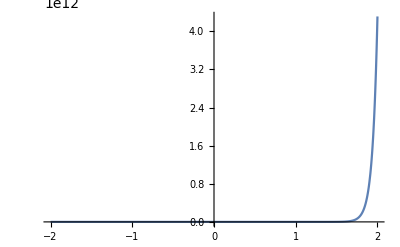

```mathematica
ClearAll[p,l,q,τ];
p=Transpose[meanI][[1]];
l=bl;
q=2.;
Plot[{gam[p,l,q,τ]},{τ,-2,2},PlotRange->All]
```

## Averaged dimensions

#### Preliminaries (diagonalization, computation of the bands, of the wave vectors...)

```mathematica
(* return bands and intensities ordered by increasing energy, for 2 consecutive sizes Subscript[F, n] and Subscript[F, n+1] *)
IntBands[n_,ρ_]:=Block[{nN=n+3,ts=1.,tw=ρ,vpp,vpa,vppN,vpaN,wfp,wfa,wfpN,wfaN,o,intensities,intensitiesN,intp,inta,intpN,intaN,bands,bandsN},

(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hp[n-2,tw,ts]];
{vpa,wfa}=Eigensystem[ha[n-2,tw,ts]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;

intensities=0.5*(intp+inta);

(* spectres des systèmes de taille i+1 p et anti-p *)
{vppN,wfpN}=Eigensystem[hp[nN-2,tw,ts]];
{vpaN,wfaN}=Eigensystem[ha[nN-2,tw,ts]];

o=Ordering[vppN];
vppN=vppN[[o]];
wfpN=wfpN[[o]];
(* intensity *)
intpN=Abs[wfpN]^2;

o=Ordering[vpaN];
vpaN=vpaN[[o]];
wfaN=wfaN[[o]];
intaN=Abs[wfaN]^2;

intensitiesN=0.5*(intpN+intaN);

(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandsN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];

{intensities,intensitiesN,bands,bandsN}]
```

In the weak quasiperiodicity limit, Γ^(n+1)/Γ^n rather than Γ^(n+3)/Γ^n.

```mathematica
(* return bands and intensities ordered by increasing energy, for 2 consecutive sizes Subscript[F, n] and Subscript[F, n+1] *)
IntBandsWeak[n_,ρ_]:=Block[{nN=n+1,ts=1.,tw=ρ,vpp,vpa,vppN,vpaN,wfp,wfa,wfpN,wfaN,o,intensities,intensitiesN,intp,inta,intpN,intaN,bands,bandsN},

(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hp[n-2,tw,ts]];
{vpa,wfa}=Eigensystem[ha[n-2,tw,ts]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;

intensities=0.5*(intp+inta);

(* spectres des systèmes de taille i+1 p et anti-p *)
{vppN,wfpN}=Eigensystem[hp[nN-2,tw,ts]];
{vpaN,wfaN}=Eigensystem[ha[nN-2,tw,ts]];

o=Ordering[vppN];
vppN=vppN[[o]];
wfpN=wfpN[[o]];
(* intensity *)
intpN=Abs[wfpN]^2;

o=Ordering[vpaN];
vpaN=vpaN[[o]];
wfaN=wfaN[[o]];
intaN=Abs[wfaN]^2;

intensitiesN=0.5*(intpN+intaN);

(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandsN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];

{intensities,intensitiesN,bands,bandsN}]
```

```mathematica
(* Averaged q-intensity *)
avInt[intlist_,q_]:=(1/Length[intlist])*Map[Plus@@((#)^q)&,Transpose[intlist]];
```

```mathematica
(* Compute τx(q) from the averaged q-intensity *)
tauqx[avint_,avintN_]:=-Log[(Plus@@avint)/(Plus@@avintN)]/Log[(Length@avint)/(Length@avintN)];
```

```mathematica
(* Compute τμ(q) from 2 consecutive (Subscript[F, n] and Subscript[F, n+3]) averaged q-intensities *)
tauqmu[avint_,avintN_,bl_,blN_]:=Block[{gammu,gammuN},
(* associated Γ function (bl is the list of bands) *)
gammu=Plus@@((avint)(bl)^-τ);
gammuN=Plus@@((avintN)(blN)^-τ);
τ/.FindRoot[gammu/gammuN-1,{τ,1.}]]
```

```mathematica
(* Compute spectral τ(qsp) *)
tauspec[qsp_,bl_,blN_]:=Block[{gamSpec,gamSpecN},
(* Fractal dimension of the spectrum *)
gamSpec=(Length@bl)^-qsp Plus@@((bl)^-τ);
gamSpecN=(Length@blN)^-qsp Plus@@((blN)^-τ);

τ/.FindRoot[gamSpecN/gamSpec-1,{τ,0.5}]
]
```

#### Focus on τmu

```mathematica
qr=Range[0.1,10.,.34];
ρ=0.9;
```

```mathematica
n=13;
{int,intN,bl,blN}=IntBands[n,ρ];
avints=ParallelMap[avInt[int,#]&,qr];
avintsN=ParallelMap[avInt[intN,#]&,qr];
τmulist13=Parallelize@MapThread[tauqmu[#1,#2,bl,blN]&,{avints,avintsN}];
```

```mathematica
n=16;
{int,intN,bl,blN}=IntBands[n,ρ];
avints=ParallelMap[avInt[int,#]&,qr];
avintsN=ParallelMap[avInt[intN,#]&,qr];
τmulist16=Parallelize@MapThread[tauqmu[#1,#2,bl,blN]&,{avints,avintsN}];
```

```mathematica
n=13;
{int,intN,bl,blN}=IntBandsWeak[n,ρ];
avints=ParallelMap[avInt[int,#]&,qr];
avintsN=ParallelMap[avInt[intN,#]&,qr];
τmulist13W=Parallelize@MapThread[tauqmu[#1,#2,bl,blN]&,{avints,avintsN}];
```

```mathematica
n=16;
{int,intN,bl,blN}=IntBandsWeak[n,ρ];
avints=ParallelMap[avInt[int,#]&,qr];
avintsN=ParallelMap[avInt[intN,#]&,qr];
τmulist16W=Parallelize@MapThread[tauqmu[#1,#2,bl,blN]&,{avints,avintsN}];
```

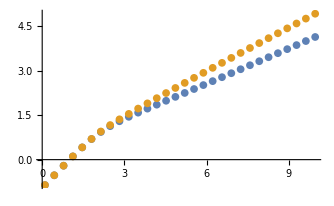

```mathematica
ListPlot[glue[qr,#]&/@{τmulist13,τmulist16},PlotRange->All]
```

```mathematica
Plus@@((τmulist13-τmulist16)^2)
```

5.47375

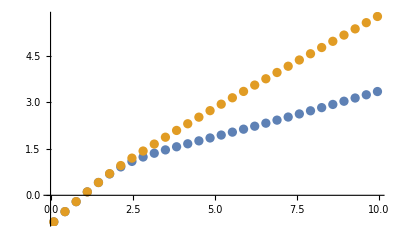

```mathematica
ListPlot[glue[qr,#]&/@{τmulist13W,τmulist16W},PlotRange->All]
```

```mathematica
τth[q_]:=If[q<2,q-1,q/2];
```

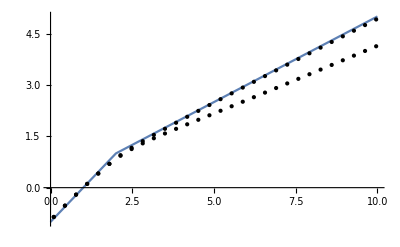

```mathematica
Plot[τth[q],{q,0,10},Epilog->{Point@glue[qr,τmulist13],Point@glue[qr,τmulist16]}]
```

#### Focus on τx

```mathematica
qr=Range[0.1,10.,.34];
ρ=0.9;
```

```mathematica
n=13;
{int,intN,bl,blN}=IntBands[n,ρ];
avints=ParallelMap[avInt[intN,#]&,qr];
τxlist13=ParallelMap[tauqx,avints];
```

```mathematica
n=16;
{int,intN,bl,blN}=IntBands[n,ρ];
avints=ParallelMap[avInt[intN,#]&,qr];
τxlist14=ParallelMap[tauqx,avints];
```

```mathematica
n=13;
{int,intN,bl,blN}=IntBandsWeak[n,ρ];
avints=ParallelMap[avInt[intN,#]&,qr];
τxlist13W=ParallelMap[tauqx,avints];
```

```mathematica
n=16;
{int,intN,bl,blN}=IntBandsWeak[n,ρ];
avints=ParallelMap[avInt[intN,#]&,qr];
τxlist14W=ParallelMap[tauqx,avints];
```

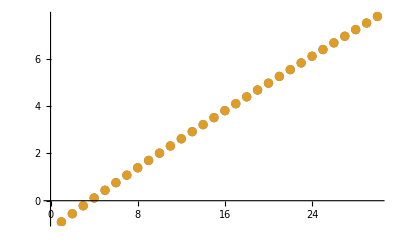

```mathematica
ListPlot[{τxlist13,τxlist14}]
```

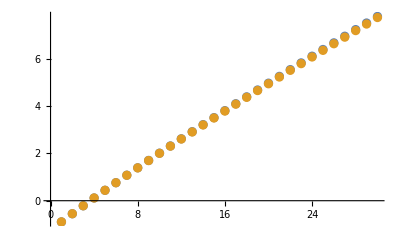

```mathematica
ListPlot[{τxlist14,τxlist14W}]
```

#### Focus on τspec

```mathematica
qr=Range[0.1,10.,.34];
ρ=0.9;
```

```mathematica
n=13;
{int,intN,bl,blN}=IntBandsWeak[n,ρ];
τspeclist1=ParallelMap[{#,tauspec[#,bl,blN]}&,qr];
```

```mathematica
n=16;
{int,intN,bl,blN}=IntBandsWeak[n,ρ];
τspeclist2=ParallelMap[{#,tauspec[#,bl,blN]}&,qr];
```

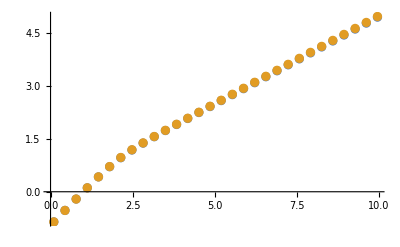

```mathematica
ListPlot[{τspeclist1,τspeclist2}]
```

#### Comparison: n_new = n+3: ρ=1/2

```mathematica
ρ=0.5;
n=13;
nN=n+3;
qr=Range[.1,10.,.2];
```

```mathematica
(* bands, intensities... *)
{int,intN,bl,blN}=IntBands[n,ρ];
```

```mathematica
{int2,intN2,bl2,blN2}=IntBands[nN,ρ];
```

```mathematica
(* list of averaged over i and weighted intensities *)
avints=ParallelMap[avInt[int,#]&,qr];
avintsN=ParallelMap[avInt[intN,#]&,qr];
```

```mathematica
(* list of averaged over i and weighted intensities *)
avints2=ParallelMap[avInt[int2,#]&,qr];
avintsN2=ParallelMap[avInt[intN2,#]&,qr];
```

```mathematica
(* τx(qr) *)
τx12=tauqx/@avintsN;
τx22=tauqx/@avintsN2;
(* deduce qspec *)
qsp12=1+τx12;
qsp22=1+τx22;
```

```mathematica
(* compute τ(qspec) *)
τsp12=ParallelMap[tauspec[#,bl,blN]&,qsp12];
τsp22=ParallelMap[tauspec[#,bl2,blN2]&,qsp22];
```

```mathematica
(* compute τμ(qr) *)
τmu12=Parallelize@MapThread[tauqmu[#1,#2,bl,blN]&,{avints,avintsN}];
τmu22=Parallelize@MapThread[tauqmu[#1,#2,bl2,blN2]&,{avints2,avintsN2}];
```

```mathematica
(* compare Dμ(qr) and Dx(qr)*D(qspec) = τ(qspec)/(qr-1) *)
dxdsp12=τsp12/(qr-1);
dxdsp22=τsp22/(qr-1);
dmu12=τmu12/(qr-1);
dmu22=τmu22/(qr-1);
```

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

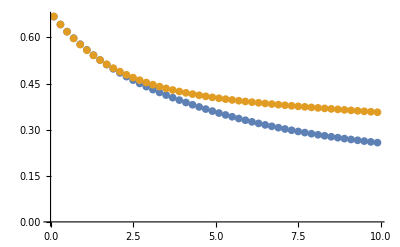

```mathematica
ListPlot[{glue[qr,dxdsp12],glue[qr,dmu12]}]
```

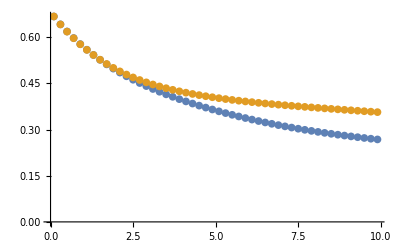

```mathematica
ListPlot[{glue[qr,dxdsp22],glue[qr,dmu22]}]
```

#### Comparison: n_new = n+3: ρ=1/10

```mathematica
ρ=0.1;
n=13;
nN=n+3;
qr=Range[.1,10.,.2];
```

```mathematica
(* bands, intensities... *)
{int,intN,bl,blN}=IntBands[n,ρ];
```

```mathematica
{int2,intN2,bl2,blN2}=IntBands[nN,ρ];
```

```mathematica
(* list of averaged over i and weighted intensities *)
avints=ParallelMap[avInt[int,#]&,qr];
avintsN=ParallelMap[avInt[intN,#]&,qr];
```

```mathematica
(* list of averaged over i and weighted intensities *)
avints2=ParallelMap[avInt[int2,#]&,qr];
avintsN2=ParallelMap[avInt[intN2,#]&,qr];
```

```mathematica
(* τx(qr) *)
τx1=tauqx/@avintsN;
τx2=tauqx/@avintsN2;
(* deduce qspec *)
qsp1=1+τx1;
qsp2=1+τx2;
```

```mathematica
(* compute τ(qspec) *)
τsp1=ParallelMap[tauspec[#,bl,blN]&,qsp1];
τsp2=ParallelMap[tauspec[#,bl2,blN2]&,qsp2];
```

```mathematica
(* compute τμ(qr) *)
τmu1=Parallelize@MapThread[tauqmu[#1,#2,bl,blN]&,{avints,avintsN}];
τmu2=Parallelize@MapThread[tauqmu[#1,#2,bl2,blN2]&,{avints2,avintsN2}];
```

```mathematica
(* compare Dμ(qr) and Dx(qr)*D(qspec) = τ(qspec)/(qr-1) *)
dxdsp1=τsp1/(qr-1);
dxdsp2=τsp2/(qr-1);
dmu1=τmu1/(qr-1);
dmu2=τmu2/(qr-1);
```

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

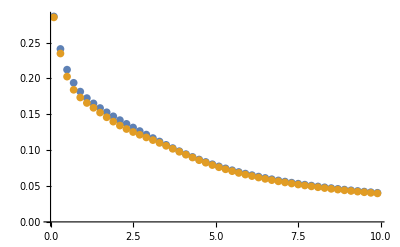

```mathematica
ListPlot[{glue[qr,dxdsp1],glue[qr,dmu1]}]
```

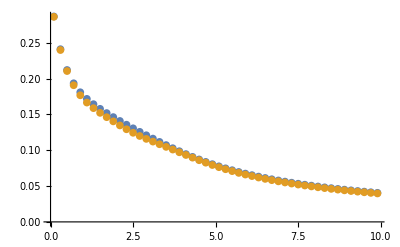

```mathematica
ListPlot[{glue[qr,dxdsp2],glue[qr,dmu2]}]
```

#### Comparison: n_new = n+3: ρ=0.9

```mathematica
ρ=0.9;
n=13;
nN=n+3;
qr=Range[.1,10.,.2];
```

```mathematica
(* bands, intensities... *)
{int,intN,bl,blN}=IntBands[n,ρ];
```

```mathematica
{int2,intN2,bl2,blN2}=IntBands[nN,ρ];
```

```mathematica
(* list of averaged over i and weighted intensities *)
avints=ParallelMap[avInt[int,#]&,qr];
avintsN=ParallelMap[avInt[intN,#]&,qr];
```

```mathematica
(* list of averaged over i and weighted intensities *)
avints2=ParallelMap[avInt[int2,#]&,qr];
avintsN2=ParallelMap[avInt[intN2,#]&,qr];
```

```mathematica
(* τx(qr) *)
τx19=Parallelize@MapThread[tauqx,{avints,avintsN}];
τx29=Parallelize@MapThread[tauqx,{avints2,avintsN2}];
(* deduce qspec *)
qsp19=1+τx19;
qsp29=1+τx29;
```

```mathematica
(* compute τ(qspec) *)
τsp19=ParallelMap[tauspec[#,bl,blN]&,qsp19];
τsp29=ParallelMap[tauspec[#,bl2,blN2]&,qsp29];
```

```mathematica
(* compute τμ(qr) *)
τmu19=Parallelize@MapThread[tauqmu[#1,#2,bl,blN]&,{avints,avintsN}];
τmu29=Parallelize@MapThread[tauqmu[#1,#2,bl2,blN2]&,{avints2,avintsN2}];
```

```mathematica
(* compare Dμ(qr) and Dx(qr)*D(qspec) = τ(qspec)/(qr-1) *)
dxdsp19=τsp19/(qr-1);
dxdsp29=τsp29/(qr-1);
dmu19=τmu19/(qr-1);
dmu29=τmu29/(qr-1);
```

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

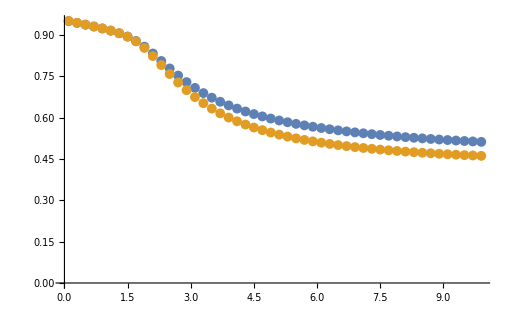

```mathematica
ListPlot[{glue[qr,dxdsp19],glue[qr,dmu19]}]
```

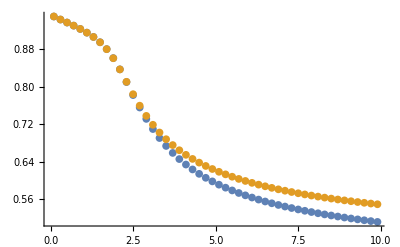

```mathematica
ListPlot[{glue[qr,dxdsp29],glue[qr,dmu29]}]
```

```mathematica
dthper[q_]:=If[q<2,1-(1-ρ)4 Pi^-2,q/(2(q-1))];
```

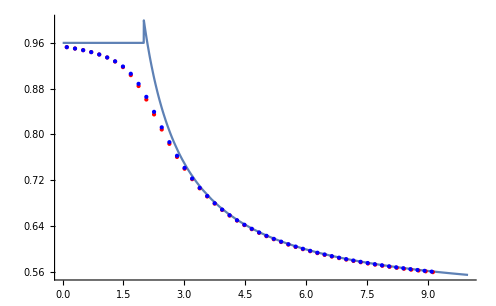

```mathematica
Plot[dthper[q],{q,0,10},Epilog->{{Red,Point@glue[qsp19,τsp19/(qsp19-1)]},{Blue,Point@glue[qsp29,τsp29/(qsp29-1)]}}]
```

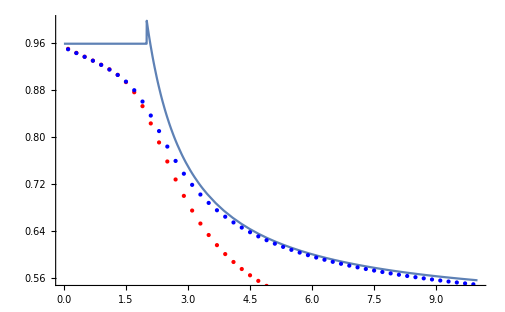

```mathematica
Plot[dthper[q],{q,0,10},Epilog->{{Red,Point@glue[qr,τmu19/(qr-1)]},{Blue,Point@glue[qr,τmu29/(qr-1)]}}]
```

#### Comparison: n_new = n+1

```mathematica
ρ=0.9;
n=13;
nN=n+3;
qr=Range[.1,10.,.2];
```

```mathematica
(* bands, intensities... *)
{int,intN,bl,blN}=IntBandsWeak[n,ρ];
```

```mathematica
{int2,intN2,bl2,blN2}=IntBandsWeak[nN,ρ];
```

```mathematica
(* list of averaged over i and weighted intensities *)
avints=ParallelMap[avInt[int,#]&,qr];
avintsN=ParallelMap[avInt[intN,#]&,qr];
```

```mathematica
(* list of averaged over i and weighted intensities *)
avints2=ParallelMap[avInt[int2,#]&,qr];
avintsN2=ParallelMap[avInt[intN2,#]&,qr];
```

```mathematica
(* τx(qr) *)
τx1w=tauqx/@avintsN;
τx2w=tauqx/@avintsN2;
(* deduce qspec *)
qsp1w=1+τx1w;
qsp2w=1+τx2w;
```

```mathematica
(* compute τ(qspec) *)
τsp1w=ParallelMap[tauspec[#,bl,blN]&,qsp1w];
τsp2w=ParallelMap[tauspec[#,bl2,blN2]&,qsp2w];
```

```mathematica
(* compute τμ(qr) *)
τmu1w=Parallelize@MapThread[tauqmu[#1,#2,bl,blN]&,{avints,avintsN}];
τmu2w=Parallelize@MapThread[tauqmu[#1,#2,bl2,blN2]&,{avints2,avintsN2}];
```

```mathematica
(* compare Dμ(qr) and Dx(qr)*D(qspec) = τ(qspec)/(qr-1) *)
dxdsp1w=τsp1w/(qr-1);
dxdsp2w=τsp2w/(qr-1);
dmu1w=τmu1w/(qr-1);
dmu2w=τmu2w/(qr-1);
```

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

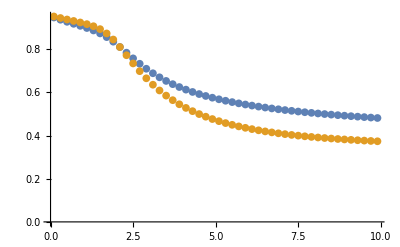

```mathematica
ListPlot[glue[qr,#]&/@{dxdsp1w,dmu1w}]
```

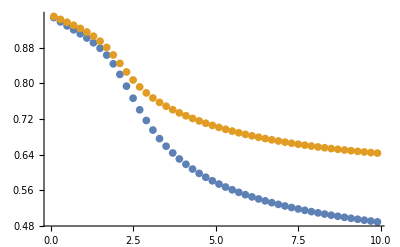

```mathematica
ListPlot[glue[qr,#]&/@{dxdsp2w,dmu2w}]
```

```mathematica
Plus@@((dxdsp1-dmu1)^2)
```

0.370558

```mathematica
Plus@@((dxdsp2-dmu2)^2)
```

0.639219

#### τmu by box counting

Compute generalized dimensions by box-counting

```mathematica
(* take a fractal set (represented as an ordered list of points between 0 and 1 each associated to a weight), return qnorm = Subscript[Σ, i] Subscript[p, i]^q, where Subscript[p, i] is the weight of the i^th box. Explicitely, Subscript[p, i] is the sum of the weights of the pts in the i^th box: Subscript[p, i] = Subscript[Σ, s∈Subscript[b, i]] Subscript[w, s].*)
Clear[WeightedBc];
WeightedBc[pts_,weights_,n_,δ_,q_]:=Block[{curLbl=1,curBS=0,Δ,b=δ^-n,qnorm=0,ntot=Length[pts],curweight=0,len=Length[pts],loop,p0},
p0=pts[[curLbl]];
(*Δ:distance btw the left side of the current box and the current pt*)
(*If[b≥p0,Δ=b-p0,Δ=Mod[p0,b]];*)
Δ=Max[b-p0,0];
(* position of the current box left side *)
curBS=p0-Δ;
While[curLbl≤len,
(* there is for now 0 pt in the current box *)
curweight=0;
(*while the current pt is in the current box, add its weight and pass to the pt on its right*)
While[Δ≤b,
curweight+=weights[[curLbl]];
curLbl++;
If[curLbl≤ len,Δ=pts[[curLbl]]-curBS,Break[]];
];
(* Subscript[p, i]^q *)
qnorm+=(curweight)^q;
If[curLbl>len,Break[]];
(*after the loop the current box has jumped of Floor[Δ/b] units*)
curBS+=b Floor[Δ/b];
Δ=pts[[curLbl]]-curBS;
];
Return[qnorm];]
```

```mathematica
(* To do. *)
(* μ: measure of probability: μ[[i]]={position of pt i, probability weight of pt i} *)
Clear[WeightedBc];
WeightedBc[μ_,n_,δ_,q_]:=Block[{curLbl=1,curBS=0,Δ,b=δ^-n,qnorm=0,ntot=Length[pts],curweight=0,len=Length[pts],loop,p0},
Return[qnorm];]
```

Average qnorm over some possible origins of the boxes. This is equivalent to making the whole data set rotate, and to average over some possible rotations.

```mathematica
(* "rotate" the 1 pt (0≤pt≤1) or a list of pts by t *)
Clear[rot];
rot[pt_,t_]:=If[pt≥t,pt-t,pt-t+1];
SetAttributes[rot,Listable];
```

```mathematica
Hold@Manipulate[ListPlot[{sp,rot[sp,r]},PlotRange->All],{r,0,1}]
```

Hold[]

```mathematica
AveragedBc[pts_,weights_,n_,δ_,q_,rotstep_]:=Block[{len=Length[pts],nrots,avqnorm=0,ptsN,weightsN,o},
If[Mod[rotstep^-1,1]≠ 0,Break[];Throw["The rotation step is uncommensurable with the number of pts in the data set."]];
nrots=IntegerPart[1/rotstep];
For[i=0,i<nrots,i++,
(* rotate the whole set of points *)
ptsN=rot[pts,i rotstep];
(* the points must be reordered by increasing position; compute the permutation that does that *)
o=Ordering[ptsN];
(* reorder the points and the associated weights *)
ptsN=ptsN[[o]];
weightsN=weights[[o]];
avqnorm+=WeightedBc[ptsN,weightsN,n,δ,q]];
avqnorm/nrots
]
```

For τ^(μ,i), the point E_a weights |ψ_(i,a)|^2.

```mathematica
intE[n_,ρ_,k_]:=Block[{ts=1.,tw=ρ,vpp,vpa,wfp,wfa,o,intp,inta},
(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hk[k,n-2,tw,ts]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

(* rescale spectrum between 0 and 1 *)
vpp=(vpp-vpp[[1]])/(vpp[[-1]]-vpp[[1]]);

{intp,vpp}
]
```

```mathematica
n=16;
ρ=.1;
{intp,sp}=intE[n,ρ,0.];
{inta,sp}=intE[n,ρ,Pi];
(* w[[i]] is the set of weights for τ^(μ,i) *)
wp=Transpose[intp];
wa=Transpose[inta];
```

```mathematica
Fibonacci[16]/2//N
```

493.5

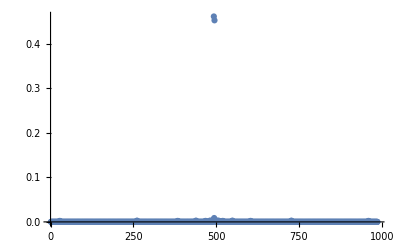

```mathematica
ListPlot[wp[[493]],PlotRange->All]
```

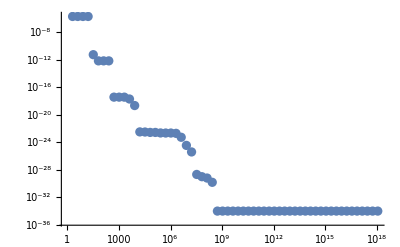

```mathematica
i=494;
q=20.;
r=Range[1,60,1.];
delta=2.;
(* compute the number of filled boxes for a whole range of values of n *)
nb=ParallelMap[WeightedBc[sp,wp[[i]],#,delta,q]&,r];
(*number of filled boxes as a function of their length*)
dat2=Parallelize@MapThread[{#1,#2}&,{delta^r,nb}];
(* the slope is the box-counting dimension of the spectrum *)
ListLogLogPlot[{dat2},PlotRange->All]
```

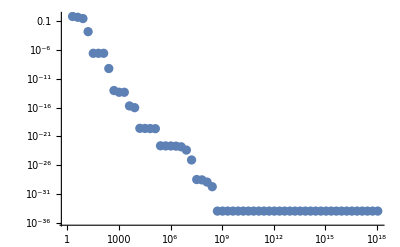

```mathematica
r=Range[1,60,1.];
delta=2.;
(* compute the number of filled boxes for a whole range of values of n *)
nb2=ParallelMap[AveragedBc[sp,wp[[i]],#,delta,q,0.1]&,r];
(*number of filled boxes as a function of their length*)
dat3=Parallelize@MapThread[{#1,#2}&,{delta^r,nb2}];
(* the slope is the box-counting dimension of the spectrum *)
ListLogLogPlot[{dat3},PlotRange->All]
```

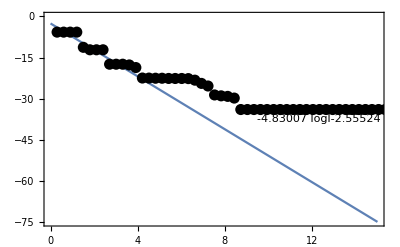

```mathematica
(* now we can fit the slope to get the box-counting dimension *)
xi=1;xf=xi+9;
fit=LinearModelFit[Log10@dat2[[xi;;xf]],logl,logl];
Plot[Normal@fit,{logl,0,15},Axes->False,Frame->True,Epilog->{PointSize@.02,Point@Log10@dat2},PlotLegends->Placed[Normal@fit,{Right,Center}]]
```

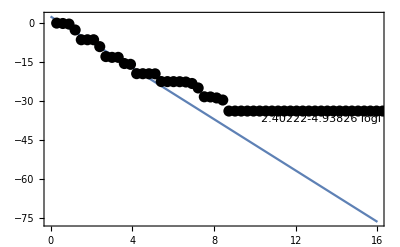

```mathematica
(* now we can fit the slope to get the box-counting dimension *)
xi=1;xf=xi+12;
fit=LinearModelFit[Log10@dat3[[xi;;xf]],logl,logl];
Plot[Normal@fit,{logl,0,16},Axes->False,Frame->True,Epilog->{PointSize@.02,Point@Log10@dat3},PlotLegends->Placed[Normal@fit,{Right,Center}]]
```

## Comparison partition function/box counting

Return the spectrum rescaled to fit into the [0,1] interval

```mathematica
spect[i_,tw_,ts_]:=Block[{spec=Sort[Eigenvalues[hp[i,tw,ts]]]},
(spec-spec[[1]])/(spec[[-1]]-spec[[1]])]
```

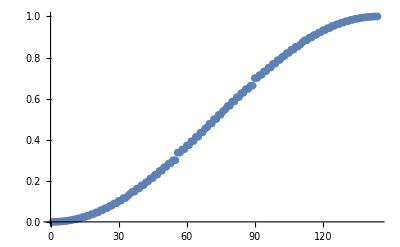

```mathematica
ListPlot@spect[10,.9,1.]
```

Compute Hausdorff dimension by box-counting

```mathematica
(* take a fractal set (represented as an ordered list of points between 0 and 1), return the number of filled boxes *)
Clear[bc];
bc[list_,n_,δ_]:=Block[{curLbl=1,curBS,Δ,b=δ^-n,nboxes=0,len=Length[list],loop},(*Δ:distance btw the left side of the current box and the current pt*)
(*Δ=list[[curLbl]]-curBS;*)
Δ=Mod[list[[curLbl]],b];
curBS=list[[curLbl]]-Δ;
While[curLbl<len,loop=False;
(*while the current pt is in the current box,pass to the pt on its right*)
While[Δ≤b&&curLbl<len,curLbl++;Δ=list[[curLbl]]-curBS;];
(*after the loop the current box has jumped of Floor[Δ/b] units,and one more box has points in it*)curBS+=b Floor[Δ/b];
nboxes++;Δ=list[[curLbl]]-curBS;];
Return[nboxes];]
```

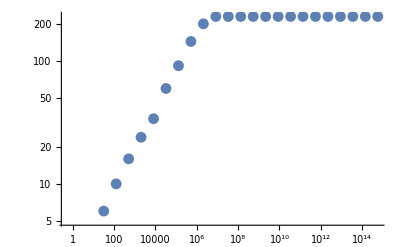

```mathematica
sp=spect[11,.1,1.];
r=Range[5,50,2];
delta=2;
(* compute the number of filled boxes for a whole range of values of n *)
nb=ParallelMap[bc[sp,#,delta]&,r];
(*number of filled boxes as a function of their length*)
dat=Parallelize@MapThread[{#1,#2}&,{delta^r,nb}];
(* the slope is the box-counting dimension of the spectrum *)
ListLogLogPlot[dat]
```

```mathematica
(* now we can fit the slope to get the box-counting dimension *)
xi=4;xf=xi+12;
fit=LinearModelFit[Log10@dat[[xi;;xf]],logl,logl];
Plot[Normal@fit,{logl,0,15},Axes->False,Frame->True,Epilog->{PointSize@.02,Point@Log10@dat},PlotLegends->Placed[Normal@fit,{Right,Center}]]
```

-Graphics-

```mathematica
FractalD[13,.1,1.,0]
```

-0.316947

Compute generalized dimensions by box-counting

```mathematica
(* take a fractal set (represented as an ordered list of points between 0 and 1), return Subscript[Σ, i] Subscript[p, i]^q, where Subscript[p, i] is the probability for a point of the set to be in the i^th box. *)
Clear[RenyiBc];
RenyiBc[list_,n_,δ_,q_]:=Block[{curLbl=1,curBS=0,Δ,b=δ^-n,qnorm=0,ntot=Length[list],npts=0,len=Length[list],loop},
(*Δ:distance btw the left side of the current box and the current pt*)
Δ=Mod[list[[curLbl]],b];
curBS=list[[curLbl]]-Δ;
While[curLbl≤len,
(* there is for now 0 pt in the current box *)
npts=0;
(*while the current pt is in the current box,pass to the pt on its right*)
While[Δ≤b,
curLbl++;
npts++;
If[curLbl≤ len,Δ=list[[curLbl]]-curBS,Break[]];
];
(* Subscript[p, i]^q *)
qnorm+=(npts/ntot)^q;
If[curLbl>len,Break[]];
(*after the loop the current box has jumped of Floor[Δ/b] units*)
curBS+=b Floor[Δ/b];
Δ=list[[curLbl]]-curBS;
];
Return[qnorm];]
```

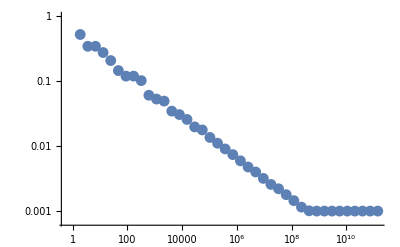

```mathematica
n=14;
ts=1.;
tw=.1;
q=2.;
sp=spect[n,tw,ts];
r=Range[1,40,1];
delta=1.9;
(* compute the number of filled boxes for a whole range of values of n *)
nb=ParallelMap[RenyiBc[sp,#,delta,q]&,r];
(*number of filled boxes as a function of their length*)
dat2=Parallelize@MapThread[{#1,#2}&,{delta^r,nb}];
(* the slope is the box-counting dimension of the spectrum *)
ListLogLogPlot[{dat2}]
```

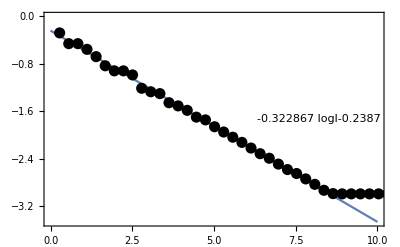

```mathematica
(* now we can fit the slope to get the box-counting dimension *)
xi=1;xf=xi+28;
fit=LinearModelFit[Log10@dat2[[xi;;xf]],logl,logl];
Plot[Normal@fit,{logl,0,10},Axes->False,Frame->True,Epilog->{PointSize@.02,Point@Log10@dat2},PlotLegends->Placed[Normal@fit,{Right,Center}]]
```

```mathematica
(* compare with calculation by partition function *)
FractalD[n,tw,ts,q]
```

0.317722

## Direct computation of α(a)

Using the definition of α:
1/F_n∼ (Δ_a^n)^(α(a)) as n→∞,
we get
α(a)  = lim_(n→∞) (log( 1/F_n ))/(log( Δ_a^n ))

```mathematica
(* Return banlists *)
BandList[i_,tw_,ts_]:=Block[{vpp,vpa,bandlist},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i,tw,ts]]];
vpa=Sort[Eigenvalues[ha[i,tw,ts]]];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlist
]
```

```mathematica
(* compute of alphas for a given set of bands *)
AllAlphas[bandlist_]:=Block[{L=Length@bandlist,alphalist},
alphalist=-Log[L]/Log[bandlist];
alphalist
]
```

```mathematica
b=BandList[17,1.,1.];
```

```mathematica
αs=AllAlphas[b];
```

Not satisfying: there are values α > 1 !!
The Legendre transform of τ(q) is performing much better.

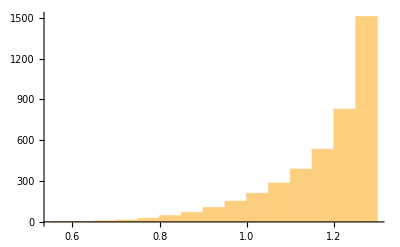

```mathematica
Histogram[αs]
```

```mathematica
(Sort@αs)[[-1]]
```

1.28273

Mean α averaged on all sites having a given x value.

```mathematica
(* n = 3p +1 *)
p=4;
n=3p+1;
nN=n+1;
(* compute Subscript[n, m] x *)
nml=nm[#,n]&/@Range[Fibonacci[n]];
nmlN=nm[#,nN]&/@Range[Fibonacci[nN]];
(* display values of Subscript[n, m] x shared by both systems *)
DeleteDuplicates[Intersection[nml,nmlN]]//Sort
(* choose among these values *)
nmol=0;
(* positions corresponding to this x value, on both systems *)
posl=Position[nml,nmol]//Flatten;
poslN=Position[nmlN,nmol]//Flatten;
```

{0,3,6}

```mathematica
(* use the PREVIOUSLY COMPUTED bandlists *)
bl[[posl]]
```

{3.69462×10^-8}

```mathematica
blN[[poslN]]
```

{3.69253×10^-9}

```mathematica
AllAlphas[bl][[posl]]
```

{0.318517}

```mathematica
Log[Fibonacci[n]/Fibonacci[n+1]]/Log[tw]
```

0.208985

```mathematica
0.32*0.00082
```

0.0002624

## Comparison asymptotically exact/numerical solution in the ρ → 0 limit.

### D_q

```mathematica
Col[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

```mathematica
(* asymptotically exact solution in the ρ->0 limit *)
exactFD[ρ_,q_]:=Block[{ω=N[1/GoldenRatio],z,barz},
z=ρ/2;
barz=ρ^2;
τ/.FindRoot[2 ω^(2q)z^-τ+ω^(3q)barz^-τ-1,{τ,1.}]
]
```

```mathematica
ClearAll[q,a];
ω=1/GoldenRatio;
z=ρ/2;
barz=ρ^2;
2 ω^(2q)z^-τ+ω^(3q)barz^-τ/.τ->-Log[a]/Log[ρ]
Limit[%,ρ->0]/.q->0
Solve[%==1,a]
```

2^(1-Log[a]/Log[ρ]) a GoldenRatio^(-2 q)+GoldenRatio^(-3 q) (ρ^2)^(Log[a]/Log[ρ])

a (2+a)

{{a→-1-√2},{a→-1+√2}}

```mathematica
err[q_]:=Block[{i=13,listρ,numd2,exactd2,dat},
(* ρ = Subscript[t, w]/Subscript[t, s] *)
listρ=Table[1.2^-it,{it,1,15}];
(* numerical Rényi entropy for ρ in listρ *)
numd2=ParallelMap[FractalD[i,#,1.,q]&,listρ];
(* asymptotically exact Rényi entropy for ρ in listρ *)
exactd2=exactFD[#,q]&/@listρ;
dat=Col[listρ^-1,Abs[numd2-exactd2]/Abs[q-1]];
(*Print[ListLogLogPlot[dat]];*)
dat
]
```

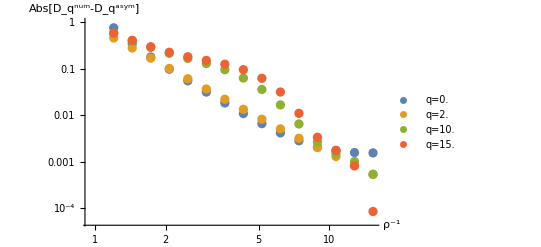

```mathematica
ListLogLogPlot[err[#]&/@#,PlotLegends->("q="<>ToString@#&/@#),AxesLabel->{"ρ^-1",Abs[Subscript[D, q]^num-Subscript[D, q]^asym]}]&@{0.,2.,10.,15.}
```

Convergence is good with Γ^(n+2)/Γ^n for q<0, and is good with Γ^(n+1)/Γ^n for q>0.

```mathematica
(* Compute the fractal dimension Subscript[D, q0] for a system of size fib(i+2) *)
Clear[FractalD2];
FractalD2[i_,tw_,ts_,q0_]:=Block[{vpp,vpa,vppN,vpaN,bandlist,bandlistN,gam,gamN,τ0},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i,tw,ts]]];
vpa=Sort[Eigenvalues[ha[i,tw,ts]]];
(* spectres des systèmes de taille i+1 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+2,tw,ts]]];
vpaN=Sort[Eigenvalues[ha[i+2,tw,ts]]];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
(* calcul des fonctions de partition Subscript[Γ, i] et Subscript[Γ, i+1] *)
gam=Fibonacci[i+2]^-q Plus@@((bandlist)^-τ);
gamN=Fibonacci[i+4]^-q Plus@@((bandlistN)^-τ);
(* Subscript[D, q0] *)
τ0=τ/.FindRoot[(gamN/gam/.q->q0)-1,{τ,0}];
τ0
]
```

```mathematica
err2[q_]:=Block[{i=11,listρ,numd2,exactd2,dat},
(* ρ = Subscript[t, w]/Subscript[t, s] *)
listρ=Table[1.2^-it,{it,1,15}];
(* numerical Rényi entropy for ρ in listρ *)
numd2=ParallelMap[FractalD2[i,#,1.,q]&,listρ];
(* asymptotically exact Rényi entropy for ρ in listρ *)
exactd2=exactFD[#,q]&/@listρ;
dat=Col[listρ^-1,Abs[numd2-exactd2]/Abs[q-1]];
(*Print[ListLogLogPlot[dat]];*)
dat
]
```

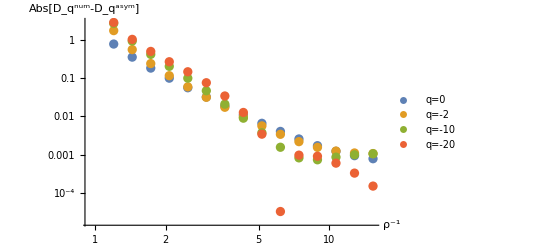

```mathematica
ListLogLogPlot[err2[#]&/@#,PlotLegends->("q="<>ToString@#&/@#),AxesLabel->{"ρ^-1",Abs[Subscript[D, q]^num-Subscript[D, q]^asym]}]&@{0,-2,-10,-20}
```

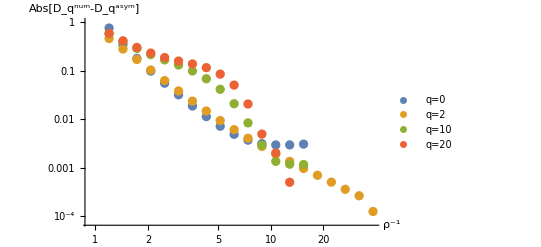

```mathematica
ListLogLogPlot[{errq0,errq2,errq10,errq20},PlotLegends->{"q="<>#&/@{"0","2","10","20"}},AxesLabel->{"ρ^-1",Abs[Subscript[D, q]^num-Subscript[D, q]^asym]}]
Export[dir<>"/data/numerical_vs_asymptotic_FD.pdf",%];
```

### q→τ(q)

```mathematica
ClearAll[f,alpha];
exactFA[ρ_]:=Block[{z=ρ/2,barz=ρ^2,ω=N[1/GoldenRatio],f,alpha},
alpha=Log[ω]/(x Log[z]+(1-2x)/3 Log[barz]);
f=(x Log[3x/2]-(1+x)Log[(1+x)^(1/3)]+(1-2x)Log[(1-2x)^(1/3)])/(x Log[z]+(1-2x)/3 Log[barz]);
{alpha,f}
]
```

```mathematica
(* asymptotically exact solution in the ρ->0 limit *)
exactFD[ρ_,q_]:=Block[{ω=1/GoldenRatio,z,barz},
z=ρ/2;
barz=ρ^2;
τ/.FindRoot[2 ω^(2q)z^-τ+ω^(3q)barz^-τ-1,{τ,1}]
]
```

```mathematica
(* Return banlists *)
Clear[BandLists];
BandLists[i_,tw_,ts_]:=Block[{vpp,vpa,vppN,vpaN,bandlist,bandlistN},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i,tw,ts]]];
vpa=Sort[Eigenvalues[ha[i,tw,ts]]];
(* spectres des systèmes de taille i+1 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+2,tw,ts]]];
vpaN=Sort[Eigenvalues[ha[i+2,tw,ts]]];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
{bandlist,bandlistN}
]
(* Return τ -> q *)
Clear[TauQ];
TauQ[τmin_,τmax_,bandlist_,bandlistN_]:=Block[{q,alpha,f,om=N[2/(1+√5)]},
(* q(τ) *)
q=Log[Plus@@((bandlistN)^-τ)/Plus@@((bandlist)^-τ)];
(*q=q/Log[Fibonacci[Length@bandlistN]/Fibonacci[Length@bandlist]];*)
q
]
```

```mathematica
{b,bnew}=BandLists[11,.1,1.];
```

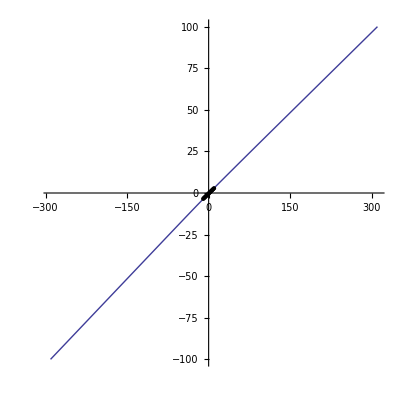

```mathematica
ParametricPlot[{TauQ[-20,20,b,bnew],τ},{τ,-100,100},AspectRatio->1,PlotRange->All,Epilog->Point@Table[{q,exactFD[.1,q]},{q,-10,10}]]
```

```mathematica
(* brute force!!!! *)
ClearAll[th,num];
num=ParallelTable[FractalFa[11,.1,1.,
```